```mathematica
(*Question 1*)
Clear["Global`*"]
Solve[Eatom-a-2*gamma*(Cos[kx*a]+Cos[ky*a])==EF,{kx,ky}]
Solve[-2*gamma*(Cos[kx*a]+Cos[ky*a])==EF,{kx,ky}]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

Solve::svars: Equations may not give solutions for all "solve" variables.

{{kx→-ArcCos[(-a+Eatom-EF-2 gamma Cos[a ky])/(2 gamma)]/a},{kx→ArcCos[(-a+Eatom-EF-2 gamma Cos[a ky])/(2 gamma)]/a}}

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

Solve::svars: Equations may not give solutions for all "solve" variables.

{{kx→-ArcCos[(-EF-2 gamma Cos[a ky])/(2 gamma)]/a},{kx→ArcCos[(-EF-2 gamma Cos[a ky])/(2 gamma)]/a}}

1

1

1

3

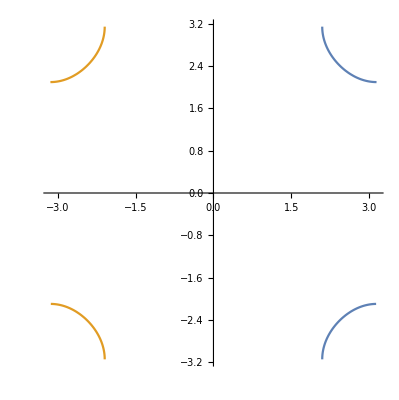

```mathematica
gamma=1
Eatom=1
a=1
EF=3
ParametricPlot[{{ArcCos[(-a+Eatom-EF-2 gamma Cos[a t])/(2 gamma)]/a,t},{(-ArcCos[(-a+Eatom-EF-2 gamma Cos[a t])/(2 gamma)])/a,t}},{t,-π,π}]
```

```mathematica
(*Question 3*)
```

```mathematica
a0=(4π*e0*hbar^2)/(m*e^2);
Ry=(m*e^4)/(8*e0^2*h^2);
hbar=h/(2π);
FullSimplify[1/a0^3*1/(√(Ry^3))]
```

(16 √2 e0^3 √((e^12 m^3)/(e0^6 h^6)) π^3)/e^6

```mathematica
(16 √2 e0^3 √((e^12 m^3)/(e0^6 h^6)) π^3)/e^6;
FullSimplify[(16 √2 e0^3 (e^(12/2) m^(3/2))/(e0^(6/2) h^(6/2)) π^3)/e^6]
```

(16 √2 m^(3/2) π^3)/h^3

```mathematica
(m^(3/2)*2^(3/2))/hbar^3
```

(16 √2 m^(3/2) π^3)/h^3

```mathematica
(*3c*)
2/(4π)^(3/2)(1.08)^(3/2)*1/(0.0529)^3*(0.026/13.6)^(3/2)
2/(4π)^(3/2)(0.7)^(3/2)*1/(0.0529)^3*(0.026/13.6)^(3/2)
```

0.0284535

0.0148473

```mathematica
(0.028453485623566786*0.014847280140914285)^(1/2)*Exp[-1.1/(2*0.026)] (*per nm3*)
(0.028453485623566786*0.014847280140914285)^(1/2)*Exp[-1.1/(2*0.026)]*(1/10^-7)^3(*per cm3*)
(0.000028453485623566786*0.000014847280140914285)^(1/2)*Exp[-1.1/(2*0.026)](*per A^3*)
```

1.33626×10^-11

1.33626×10^10

1.33626×10^-14

```mathematica
(*Question 5*)
```

```mathematica
44-44/2-1/2(25.7)*Log[(0.02845*(1/10^-7)^3)/(4*10^17)]
```

-32.798

```mathematica
Exp[-32.8/25.7]
1/(Exp[32.8/25.7]+1)
```

0.279078

0.218187

```mathematica
-45/2+1/2*(25.7)*Log[(0.0148473*(1/10^-7)^3)/(8*10^15)]
```

74.2108